```mathematica
Clear[x];
```

## Fitting

```mathematica
Clear[fittingFunction];
fittingFunction[drate_:1,power_:0,xbeta_:1.2,xMin_:-10,xMax_:20,exp_:2,expMin_:-5,expMax_:5]:=Module[{debug=0,xx,ee,mat,val,wvec,amat,bvec,coeff,errors,funX},
(* 
Grid point for fitting 
*)
xx=N[Table[xbeta^i,{i,xMin,xMax}]];
If[debug>0,
	Print["X=",Length[xx],"\n",xx]
];
(* 
Exponents 
*)
ee=N[Table[exp^j,{j,expMin,expMax}]];
If[debug>0,
	Print["Lambda=",Length[ee],"\n",ee];
	Print["Nexp,Npoint=",{Length[ee],Length[xx]}];
];
(* 
Start Fitting:(M*w*Mt)*x=(M*w*c),M=Basis(t,p) 
*)
(* dimM=nexp*npoint *)
mat=Table[Table[N[BesselK[0,ee[[j]]*xx[[i]]]],
{i,1,Length[xx]}],
{j,1,Length[ee]}];
(* dimB=npoint *)
val=Table[N[1/xx[[i]]]^drate,{i,1,Length[xx]}];
If[debug>0,
	Print[Dimensions[mat],Dimensions[val]];
];
(* Solve *)
wvec=Table[xx[[i]]^power,{i,1,Length[xx]}];
amat=mat.DiagonalMatrix[wvec].Transpose[mat];
bvec=mat.(wvec*val);
If[debug>0,
	Print[Dimensions[amat],Dimensions[bvec]];
];
coeff=PseudoInverse[amat].bvec;
(* Errors: errors=Abs[1/x-funX]/.x->xx *)
errors=Abs[coeff.mat-val];
If[debug>-1,
Print["X=",{Length[xx],Min[xx],Max[xx]}];
Print["E=",{Length[ee],Min[ee],Max[ee]}];
Print["Max|Error|=",Max[errors]]
];
(* Final *)
funX=Table[BesselK[0,x*ee[[j]]],{j,1,Length[ee]}].coeff;
funX
]
```

## Plot

```mathematica
fit1=fittingFunction[2]
```

X={31,0.161506,38.3376}

E={11,0.03125,32.}

Max|Error|=0.000383921

0.00270881 BesselK[0,0.03125 x]-0.00370873 BesselK[0,0.0625 x]+0.0234987 BesselK[0,0.125 x]+0.0229155 BesselK[0,0.25 x]+0.204213 BesselK[0,0.5 x]+0.645318 BesselK[0,1. x]+2.85315 BesselK[0,2. x]+10.929 BesselK[0,4. x]+44.8087 BesselK[0,8. x]+175.21 BesselK[0,16. x]+741.652 BesselK[0,32. x]

```mathematica
fit2=fittingFunction[2,0,1.2,-10,50,2,-10,5]
```

X={61,0.161506,9100.44}

E={16,0.000976563,32.}

Max|Error|=0.0003839

-0.0000827338 BesselK[0,0.000976563 x]+0.000475957 BesselK[0,0.00195313 x]-0.00134489 BesselK[0,0.00390625 x]+0.00280563 BesselK[0,0.0078125 x]-0.0045224 BesselK[0,0.015625 x]+0.00789556 BesselK[0,0.03125 x]-0.00785032 BesselK[0,0.0625 x]+0.0259393 BesselK[0,0.125 x]+0.0217232 BesselK[0,0.25 x]+0.204766 BesselK[0,0.5 x]+0.645043 BesselK[0,1. x]+2.85331 BesselK[0,2. x]+10.9288 BesselK[0,4. x]+44.8088 BesselK[0,8. x]+175.209 BesselK[0,16. x]+741.653 BesselK[0,32. x]

```mathematica
fit3=fittingFunction[2,1,1.2,-10,80,2,-10,10]
```

X={91,0.161506,2.16023×10^6}

E={21,0.000976563,1024.}

Max|Error|=0.000464708

1.12917×10^-6 BesselK[0,0.000976563 x]+5.97393×10^-6 BesselK[0,0.00195313 x]-9.92913×10^-6 BesselK[0,0.00390625 x]+0.000107724 BesselK[0,0.0078125 x]+6.35729×10^-6 BesselK[0,0.015625 x]+0.00103793 BesselK[0,0.03125 x]+0.00195093 BesselK[0,0.0625 x]+0.012378 BesselK[0,0.125 x]+0.0401707 BesselK[0,0.25 x]+0.179789 BesselK[0,0.5 x]+0.679225 BesselK[0,1. x]+2.80477 BesselK[0,2. x]+11.0041 BesselK[0,4. x]+44.6685 BesselK[0,8. x]+175.589 BesselK[0,16. x]+739.649 BesselK[0,32. x]+7.72395 BesselK[0,64. x]+0.000234936 BesselK[0,128. x]+1.81319×10^-13 BesselK[0,256. x]+1.42141×10^-31 BesselK[0,512. x]+1.23125×10^-67 BesselK[0,1024. x]

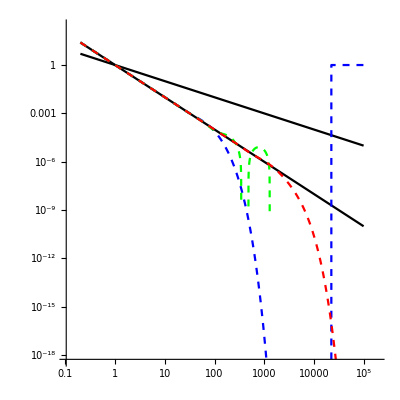

```mathematica
LogLogPlot[
{1/x,1/x^2,fit1,fit2,fit3},{x,0.2,10^5},PlotStyle->{Black,Black,{Blue,Dashed},{Green,Dashed},{Red,Dashed}},AspectRatio->1,
Frame->Automatic
]
```

```mathematica
d=2
```

2

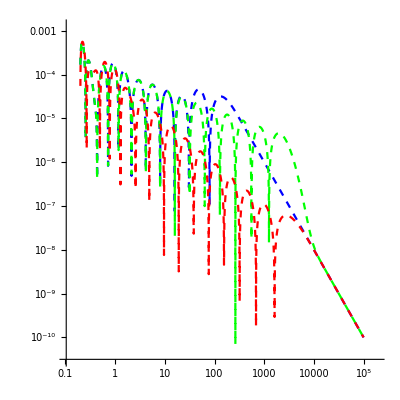

```mathematica
LogLogPlot[
{Abs[fit1-1/x^d],Abs[fit2-1/x^d],Abs[fit3-1/x^d]},{x,0.2,10^5},PlotStyle->{{Blue,Dashed},{Green,Dashed},{Red,Dashed}},AspectRatio->1,
Frame->Automatic
]
```